```mathematica
filesAR=FileNames["/home/carla/GDC/LYE/GDC_Conf_AR_LYE_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/LYE/GDC_Conf_BR_LYE_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]]
zAR=confAR[[All,2]][[All,1]]
fAR=confAR[[All,3]][[All,1]]
```

{0.000138939,0.000138939,0.00492611,0.030303,0.030303,0.0196078,0.125,1.}

{6.21355×10^-6,0.0000111358,0.00478947,0.0301736,0.0302138,0.0195514,0.124949,1.}

{0.0228722,0.0417472,0.946023,0.991496,0.994127,0.994259,0.999191,1}

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.000138939,0.000138939,0.00492611,0.00112233,0.0146085,0.00512821}

{0.0000111358,0.0000172691,0.00479332,0.00109527,0.0145517,0.0050707}

{0.0417472,0.0662643,0.947503,0.952909,0.992262,0.977821}

```mathematica
sList={1,2,3,4,5,6,7,8};
sList2={1.5,2.5,3.5,4.5,5.5,6.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];

dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&,ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&,ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&, ran2];
```

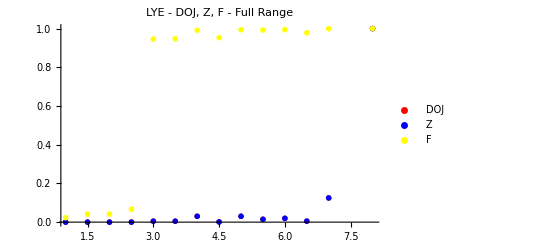

```mathematica
PlotAllParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"LYE - DOJ, Z, F - Full Range", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

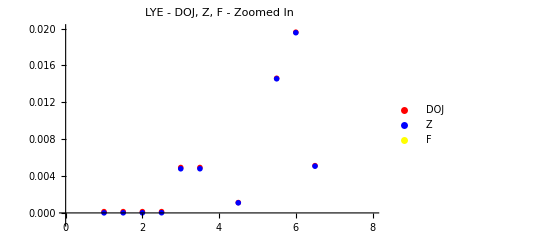

```mathematica
PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{-0.001, 0.02},  PlotLabel->"LYE - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/LYE/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"LYE_DOJ.txt"]
Put[Union[zPAR,zPBR],"LYE_Z.txt"]
Put[Union[fPAR,fPBR],"LYE_F.txt"]
Export["LYE_ALL.jpeg",PlotAllParts,ImageSize->850]
Export["LYE_Zoomed_In.jpeg",PlotParts,ImageSize->850]
```

LYE_ALL.jpeg

LYE_Zoomed_In.jpeg